```mathematica
Clear["Global`*"]
```

```mathematica
f[λ_,r_,Δ_,t_,z_]:=Evaluate[FullSimplify[F[z,t]/.First[DSolve[{λ (r (z-1)^2-1/2 Δ (z^2-1)) D[F[z,t], z]==D[F[z,t], t],F[z,0]==z},F,{z,t}]],Assumptions->{λ>0,r>0,r<1/2,Δ>0,t≥0}]]
f0[λ_,r_,Δ_,t_,z_]:=Evaluate[Limit[f[λ,r,δ,t,z],δ->0]]
```

```mathematica
g[λ_,r_,Δ_,t_,z_]:=Exp[λ Δ NIntegrate[f[λ,r,Δ,τ,z]-1,{τ,0,t}]]
```

```mathematica
h[λ_,r_,Δ_,t_,z_]:=0.95 f[λ,r,Δ,t,z]+0.05 f[λ,r,Δ,t,z] g[λ,r,Δ,t,z]
```

```mathematica
p[f_,λ_,r_,Δ_,t_,M_]:=InverseFourier[Table[f[λ,r,Δ,t,Exp[(2 π ⅈ n)/M]],{n,0,M-1}]]/(√M)
```

```mathematica
condPb[{p0_,ps___}]:={ps}/(1-p0)
```

```mathematica
cumprob[ps_]:=1-FoldList[Plus,0,ps]
```

```mathematica
Limit[D[f[λ,r,Δ,t,z], z],z->1]
```

ⅇ^(-t Δ λ)

```mathematica
Δ λ ∫_0^t Limit[D[f[λ,r,Δ,τ,z], z],z->1]ⅆτ
```

1-ⅇ^(-t Δ λ)

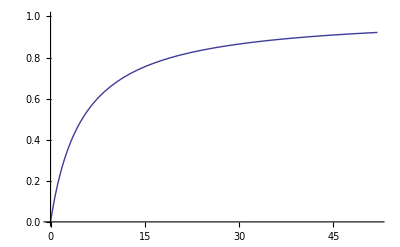

```mathematica
Plot[h[0.77,0.25,0.01,t,0],{t,0,52},PlotRange->{0,1}]
```

```mathematica
hplot=ListLogPlot[Table[Tooltip[MapThread[{#1,#2}&,{Range[0,Floor[10 t]]/(t/2),cumprob[condPb[p[h,0.77,1/4,1/100,t,Floor[10 t]+1]]]}],t],{t,{3/7,10/7,3,6,12,26,52}}],Joined->True,PlotRange->{{0,5},{1/10^3,1}}];
```

```mathematica
fplot=ListLogPlot[Table[Tooltip[MapThread[{#1,#2}&,{Range[0,Floor[10 t]]/(t/2),cumprob[condPb[p[f0,0.77,1/4,1/100,t,Floor[10 t]+1]]]}],t],{t,{3/7,10/7,3,6,12,26,52}}],Joined->True,PlotRange->{{0,5},{1/10^3,1}}];
```

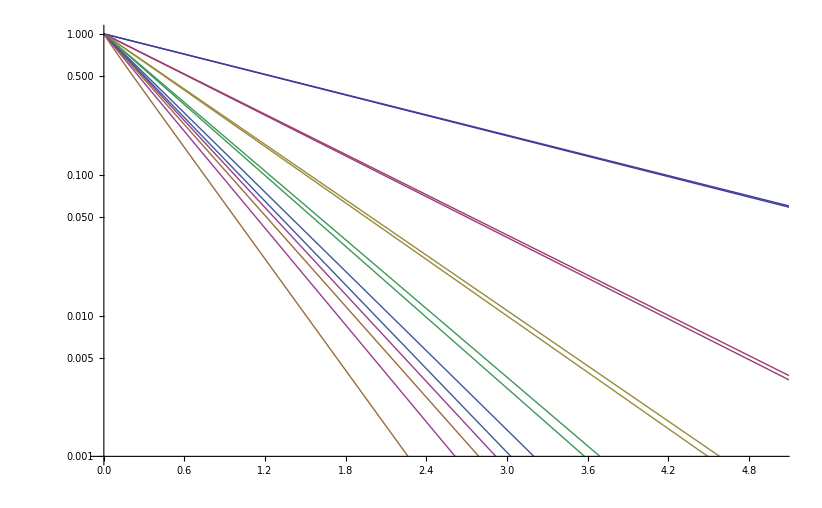

```mathematica
Show[fplot,hplot]
```